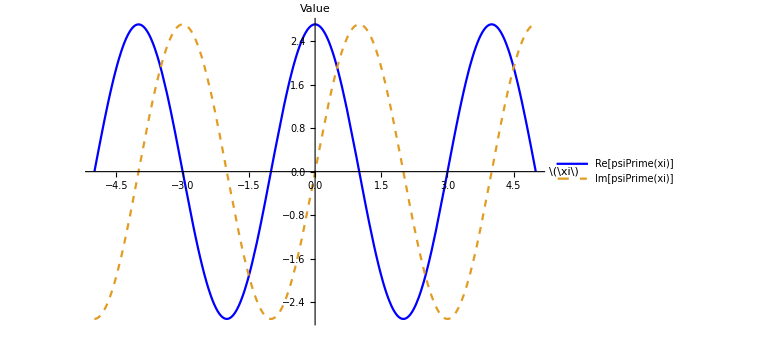

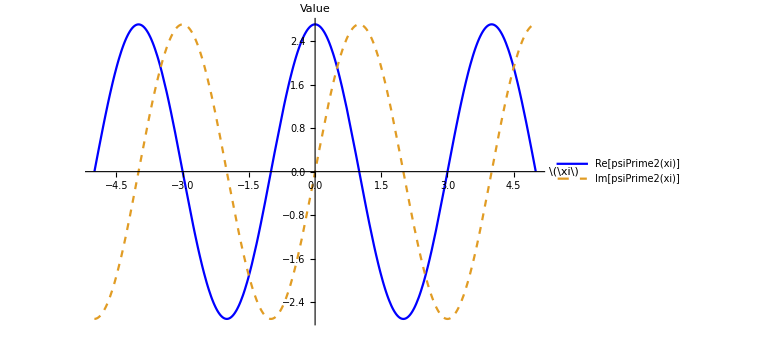

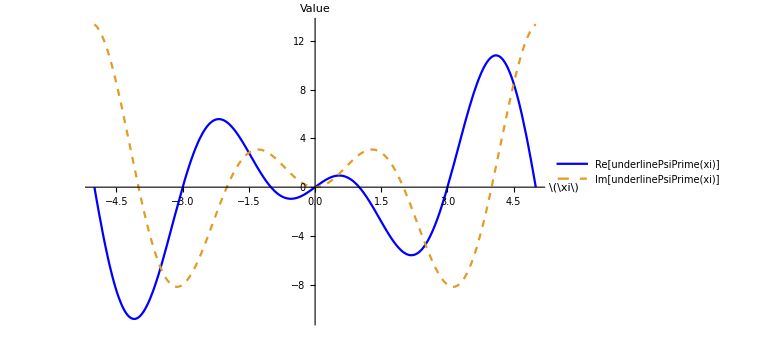

```mathematica
ClearAll["Global`*"];

(*Simplified Parameters directly in the equation*)
(*First wavefunction*)
psiPrime[xi_]:=(I+I/(100+xi))^(1 (100+xi));

(*Plotting the first psi' wavefunction*)
psiPrimePlot=Plot[{Re[psiPrime[xi]],Im[psiPrime[xi]]},{xi,-5,5},PlotStyle->{{Blue,Thick},{Gold,Dashed}},PlotRange->All,AxesLabel->{"\(\xi\)","Value"},PlotLegends->{"Re[psiPrime(xi)]","Im[psiPrime(xi)]"},ImageSize->Large];
psiPrimePlot

(*Second wavefunction*)
psiPrime2[xi_]:=(I+I/(100+xi))^(1 (100+xi));

(*Plotting the second psiPrime2 wavefunction*)
psiPrime2Plot=Plot[{Re[psiPrime2[xi]],Im[psiPrime2[xi]]},{xi,-5,5},PlotStyle->{{Blue,Thick},{Gold,Dashed}},PlotRange->All,AxesLabel->{"\(\xi\)","Value"},PlotLegends->{"Re[psiPrime2(xi)]","Im[psiPrime2(xi)]"},ImageSize->Large];
psiPrime2Plot

(*Third wavefunction,using similar structure*)
underlinePsiPrime[x_]:=(100^2)*(((1+1/(100+x))^((100+x)))-(((1+1/(100-x))^((100-x)))));

(*Plotting the underline psi' wavefunction*)
underlinePsiPrimePlot=Plot[{Re[underlinePsiPrime[x]],Im[underlinePsiPrime[x]]},{x,-5,5},PlotStyle->{{Blue,Thick},{Gold,Dashed}},PlotRange->All,AxesLabel->{"\(\xi\)","Value"},PlotLegends->{"Re[underlinePsiPrime(xi)]","Im[underlinePsiPrime(xi)]"},ImageSize->Large];
underlinePsiPrimePlot
```